Pontos de Lagrange (coordenadas adimensionais):

Ponto | Coordenadas (x,y)
L1 | 0.836900200250095211248269012637
0
L2 | 1.1556938315211141885932939291
0
L3 | -1.00506390970789172352096216074
0
L4 | 0.48784638085912788269537724015
(√3)/2
L5 | 0.48784638085912788269537724015
-(√3)/2

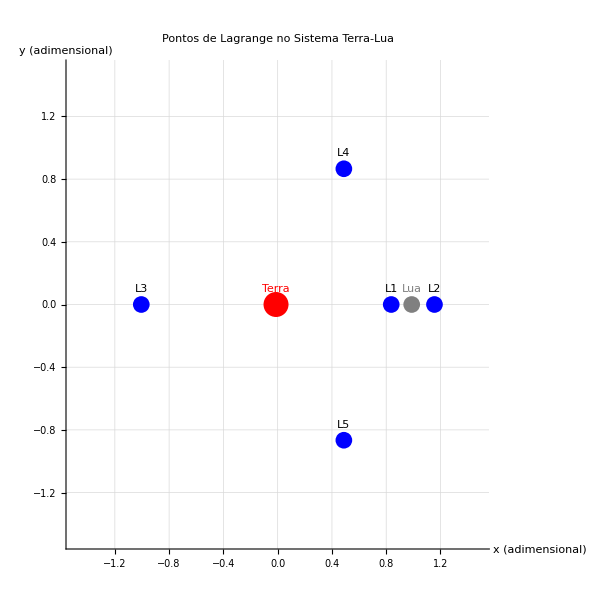

```mathematica
(*Definindo os parâmetros do sistema Terra-Lua com alta precisão*)EarthMass=5.97219`30*10^24;    (*kg*)
MoonMass=7.34767309`30*10^22;  (*kg*)
alpha=MoonMass/(EarthMass+MoonMass);

(*Distâncias adimensionais*)
d1[x_,y_]:=Sqrt[(x+alpha)^2+y^2];  (*Distância à Terra*)
d2[x_,y_]:=Sqrt[(x-(1-alpha))^2+y^2]; (*Distância à Lua*)

(*Potencial efetivo*)
U[x_,y_]:=-((1-alpha)/d1[x,y])-(alpha/d2[x,y])-(1/2)*(x^2+y^2);

(*Equações para encontrar os pontos de Lagrange*)
eqLx=x-(1-alpha)*(x+alpha)/d1[x,y]^3-alpha*(x-(1-alpha))/d2[x,y]^3;
eqLy=y-(1-alpha)*y/d1[x,y]^3-alpha*y/d2[x,y]^3;

(*Encontrando os pontos colineares (L1,L2,L3) com precisão consistente*)
(*L1 entre Terra e Lua*)
L1Solution=FindRoot[SetPrecision[x-(1-alpha)/(x+alpha)^2+alpha/(x-(1-alpha))^2==0,30],{x,SetPrecision[1-alpha-0.1,30]},WorkingPrecision->30];

(*L2 além da Lua*)
L2Solution=FindRoot[SetPrecision[x-(1-alpha)/(x+alpha)^2-alpha/(x-(1-alpha))^2==0,30],{x,SetPrecision[1-alpha+0.1,30]},WorkingPrecision->30];

(*L3 oposto à Lua*)
L3Solution=FindRoot[SetPrecision[x+(1-alpha)/(x+alpha)^2+alpha/(x-(1-alpha))^2==0,30],{x,SetPrecision[-alpha-1,30]},WorkingPrecision->30];

(*Pontos triangulares (L4 e L5)*)
L4={1/2-alpha,Sqrt[3]/2};
L5={1/2-alpha,-Sqrt[3]/2};

(*Coletando todos os pontos*)
LagrangePoints={{"L1",{x/. L1Solution,0}},{"L2",{x/. L2Solution,0}},{"L3",{x/. L3Solution,0}},{"L4",L4},{"L5",L5}};

(*Visualização do sistema*)
LagrangePlot=Show[Graphics[{{Red,PointSize[0.03],Point[{-alpha,0}],Text["Terra",{-alpha,0.1}]},{Gray,PointSize[0.02],Point[{1-alpha,0}],Text["Lua",{1-alpha,0.1}]},{Blue,PointSize[0.02],Point[#[[2]]&/@LagrangePoints]},MapThread[Text[#1,{#2[[1]],#2[[2]]+0.1}]&,{First/@LagrangePoints,Last/@LagrangePoints}]}],PlotRange->{{-1.5,1.5},{-1.5,1.5}},Axes->True,AxesLabel->{"x (adimensional)","y (adimensional)"},PlotLabel->"Pontos de Lagrange no Sistema Terra-Lua",GridLines->Automatic,ImageSize->600];

(*Exibindo os resultados*)
Print["Pontos de Lagrange (coordenadas adimensionais):"];
TableForm[LagrangePoints,TableHeadings->{None,{"Ponto","Coordenadas (x,y)"}}]

Print[LagrangePlot];
```

Gráfico salvo na área de trabalho como:

C:\Users\DELL\Desktop\PontosLagrange_TCC.pdf

C:\Users\DELL\Desktop\PontosLagrange_TCC.png

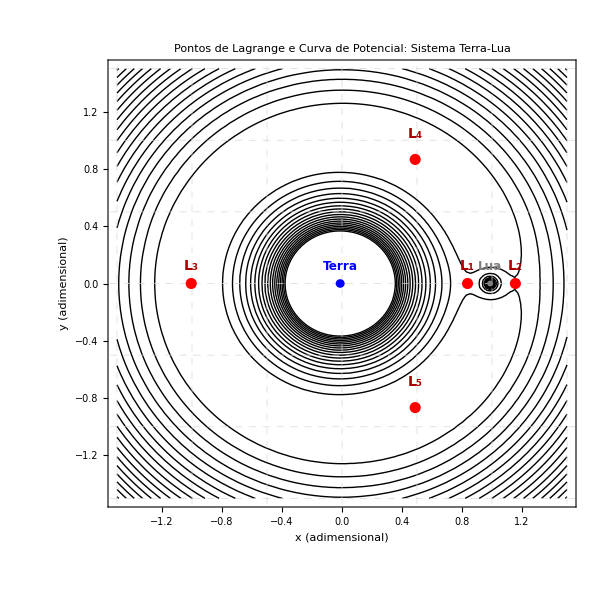

```mathematica
(*Parâmetros do sistema Terra-Lua com alta precisão*)EarthMass=5.97219`30*10^24;    (*kg*)
MoonMass=7.34767309`30*10^22;  (*kg*)
alpha=MoonMass/(EarthMass+MoonMass);

(*Funções auxiliares*)
d1[x_,y_]:=Sqrt[(x+alpha)^2+y^2];
d2[x_,y_]:=Sqrt[(x-(1-alpha))^2+y^2];
U[x_,y_]:=-((1-alpha)/d1[x,y])-(alpha/d2[x,y])-(1/2)*(x^2+y^2);

(*Cálculo dos pontos de Lagrange*)
L1Solution=FindRoot[x-(1-alpha)/(x+alpha)^2+alpha/(x-(1-alpha))^2==0,{x,1-alpha-0.1},WorkingPrecision->30];
L2Solution=FindRoot[x-(1-alpha)/(x+alpha)^2-alpha/(x-(1-alpha))^2==0,{x,1-alpha+0.1},WorkingPrecision->30];
L3Solution=FindRoot[x+(1-alpha)/(x+alpha)^2+alpha/(x-(1-alpha))^2==0,{x,-alpha-1},WorkingPrecision->30];

(*Pontos de Lagrange*)
LagrangePoints={{"L₁",{x/. L1Solution,0}},{"L₂",{x/. L2Solution,0}},{"L₃",{x/. L3Solution,0}},{"L₄",{1/2-alpha,Sqrt[3]/2}},{"L₅",{1/2-alpha,-Sqrt[3]/2}}};

(*Gráfico profissional para TCC*)
lagrangePlot=Show[ContourPlot[U[x,y],{x,-1.5,1.5},{y,-1.5,1.5},Contours->20,ContourShading->None,ContourStyle->Directive[Black,Thin],PlotRange->{{-1.5,1.5},{-1.5,1.5}}],Graphics[{{Blue,Disk[{-alpha,0},0.03],Text[Style["Terra",12,Bold,FontFamily->"Times"],{-alpha,0.12}]},{Gray,Disk[{1-alpha,0},0.02],Text[Style["Lua",12,Bold,FontFamily->"Times"],{1-alpha,0.12}]},(*Pontos de Lagrange-CORREÇÃO AQUI*){Red,AbsolutePointSize[8],Point[#[[2]]&/@LagrangePoints]},(*Rótulos*)MapThread[Text[Style[#1,14,Bold,Darker[Red],FontFamily->"Times"],{#2[[1]],#2[[2]]+If[#2[[2]]==0,0.12,0.18]}]&,{First/@LagrangePoints,Last/@LagrangePoints}]}],Frame->True,FrameLabel->{Style["x (adimensional)",14,FontFamily->"Times"],Style["y (adimensional)",14,FontFamily->"Times"]},PlotLabel->Style["Pontos de Lagrange e Curva de Potencial: Sistema Terra-Lua",16,Bold,FontFamily->"Times"],GridLines->{Range[-1.5,1.5,0.5],Range[-1.5,1.5,0.5]},GridLinesStyle->Directive[LightGray,Dashed],ImageSize->600,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->12},FrameStyle->Directive[Black,Thick]];
(*Determinar caminho da área de trabalho*)
desktopPath=FileNameJoin[{$HomeDirectory,"Desktop"}]; (*Windows*)
(*Para macOS:FileNameJoin[{$HomeDirectory,"Desktop"}]*)
(*Para Linux:FileNameJoin[{$HomeDirectory,"Desktop"}]*)

(*Exportar para a área de trabalho*)
Export[FileNameJoin[{desktopPath,"PontosLagrange_TCC.pdf"}],lagrangePlot,ImageResolution->600];
Export[FileNameJoin[{desktopPath,"PontosLagrange_TCC.png"}],lagrangePlot,ImageResolution->300];

(*Exibir o gráfico*)
Print["Gráfico salvo na área de trabalho como:"];
Print[FileNameJoin[{desktopPath,"PontosLagrange_TCC.pdf"}]];
Print[FileNameJoin[{desktopPath,"PontosLagrange_TCC.png"}]];

lagrangePlot
```